```mathematica
(*Mathematica*)
```

```mathematica
g[x_,n_]:=(1+ChebyshevU[n,2*x-1])/2^n
```

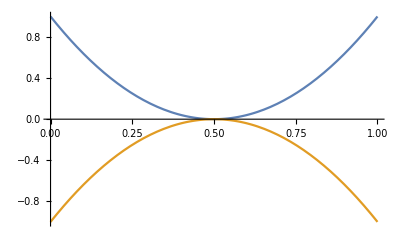

```mathematica
Plot[{g[x,2],-g[x,2]},{x,0,1}]
```

```mathematica
(* Harmonics scale  2^(n)*)
```

```mathematica
gout=Show[ParallelTable[Plot[{g[x,n],-g[x,n]},{x,0,1},ImageSize->2000,PlotRange->All,AspectRatio->1,ColorFunction->Hue,Background->Black],{n,8}]];
```

```mathematica
Export["ChebyshevU_Harmonics_scale2_Plus_Minus_colors_Level8_BackgroundBlack.jpg",gout]
```

```mathematica
(*end*)
```